THIS IS A PROOF OF CONCEPT AND IT IS NOT MEANT TO BE USED TO ACTUALLY HEAVY EVALUATE THE SAMPLER BUT TO PROTOTYPE IT EXTEND IT AND MODEL IT ..USE THE C/C++ COMPILED STUFF FOR HEAVY EVAL AS IT WILL RETURN EXACTLY THE SAME NUMBERS AS THIS VERY ONE

```mathematica
ClearAll["Global`*"]
```

Reference python implementation : Bart Wronski

```mathematica
randomSpherePoints[npts_]:=Module[{numpts=npts},
SeedRandom[1234];
a=RandomReal[2.0*Pi,numpts];
r=RandomReal[1,numpts];
aSinR=Apply[Sin, {a}]*r;
aCosR=Apply[Cos,{a}]*r;
Transpose[{aSinR,aCosR}]
]
(*ListPlot[randomSpherePoints[4096],AspectRatio->Automatic]*)
(*See this is for random points on a sphere.. https://twitter.com/fermatslibrary/status/1238088369420357633*)
```

```mathematica
randomSpherePoints2D[nbpts_]:=Block[{},
f[]:=Block[{u,t,r},
u=RandomReal[]+RandomReal[];
t=RandomReal[] 2 Pi;
r=If[u>1,2-u,u];
{r Cos[t],r Sin[t]}
];

ParallelTable[f[],nbpts]
]
(*ListPlot[randomSpherePoints2D[4096],AspectRatio->Automatic]*)
```

```mathematica
randomProject[ra_]:=Module[{r=ra,a,m},
a=RandomReal[Pi];
m=List[{Sin[a],Cos[a]},{Cos[a],-Sin[a]}];
Dot[m,r]
]
```

```mathematica
linSpace[x0_,x1_,n_]:=Range[x0,x1,(x1-x0)/(n-1)];

radonTransform[nb_]:=Block[{x,pdf,cdf},
pDF[xx_]:=Sqrt[1-xx^2];

x=linSpace[-1,1,nb];(*this should be outside ... *)
pdf=pDF[x];
cdf=Accumulate[pdf];
cdf=cdf/cdf[[-1]];
{x,cdf}
]
```

```mathematica
Clear[xp,yp];
xp={1,2,3};
yp={3,2,0};
(*transposed pts coords become .. 1,3 ; 2,2 ; 3,0*)

interpLists[x_,xl_List,yl_List]:=Block[{lst,f},
lst=Transpose[{xl,yl}];
lst=Union[lst,SameTest->(#1[[1]]==#2[[1]]&)];(*filter duplicates, aka works like numpy.interp()*)
f=Interpolation[lst,InterpolationOrder->1];
f[x]
]
(*interpLists[1.2,xp,yp]*)

(*compiling this.. as it's freaking slow*)
interpListsC = Compile[{x,xl,yl},Block[{lst,f},
lst=Transpose[{xl,yl}];
lst = Mean/@GatherBy[lst,First];(*can't use the pattern above with Compile..*)
f=Interpolation[lst,InterpolationOrder->1];
f[x]
]];
```

```mathematica
uniformizeSlice[ap_, ax_, acdf_]:=Module[{p=ap,x=ax,cdf=acdf},
p[[1]]=interpListsC[ p[[1]],x,cdf ];
inds=Ordering[ p[[1]] ];
len=Length[p[[1]]];
p[[1,inds]]=p[[1,inds]] *0.5+0.5*linSpace[0.5/len,1-0.5/len,len];
p[[1]]=interpListsC[ p[[1]],cdf,x ];
p
]
```

{3.50459,Null}

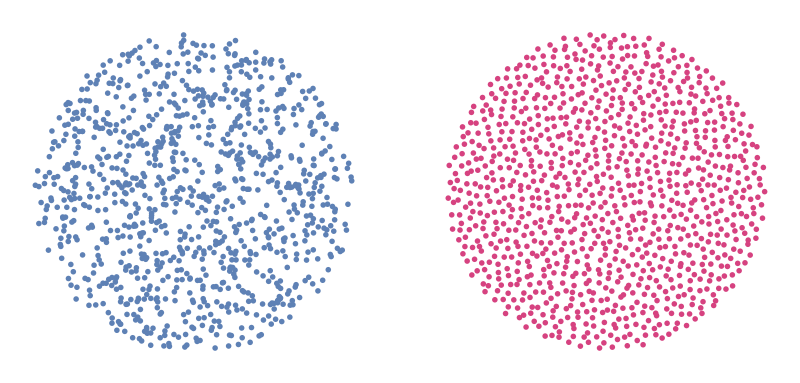

```mathematica
Clear[ggx,k];
nbPts = 1024;
ggx=radonTransform[nbPts]//N;

k= Transpose[randomSpherePoints2D[nbPts]];
(*
oo=RandomReal[{-1,1},1024];
pp=RandomReal[{-1,1},1024];
k={oo,pp};
*)
lp1=ListPlot[Transpose[k],AspectRatio->Automatic, PlotStyle->PointSize[0.01], AxesLabel->None,Axes->False,LabelStyle->Opacity[0]];

kk=k;

Quiet[
Do[
(
k=randomProject[k];
k=uniformizeSlice[k,ggx[[1]] ,ggx[[2]] ];
),500
];//AbsoluteTiming
]

lp2=ListPlot[Transpose[k],AspectRatio->Automatic, PlotStyle->{PointSize[0.01],RGBColor[0.84,0.26,0.5]}, AxesLabel->None,Axes->False,LabelStyle->Opacity[0]];

GraphicsRow[{lp1,lp2},ImageSize->Full]
```